Supplemental Material for  “Beyond Quantum Mechanics: Local QM SpaceTime
Algebra Prediction of the Singlet State” 
Validation of the Local QM Product Calculation Prediction replacing Pauli Matrices 
with SpaceTime Algebra and 2D Vectors, Based on Joy Christian’s 3-Sphere Model.
This makes the calculation real; no probabilities.  https://einstein-physics.org/

Local Quantum Mechanical Prediction of the Singlet
State Using SpaceTime Algebra
Created by Carl Diether  Feb. 2026
Caveat:  This is a simulation of a QM prediction; it is not a simulation of an experiment.

Load Clifford Package, Set Run Time Parameters, Initialize Arrays

```mathematica
<<"clifford.m"
Clear[$SetSignature];
$SetSignature={1,3};  (*Signature set for SpaceTime Algebra*)
γ0=e[1];γ1=e[2];γ2=e[3];γ3=e[4];
σ1=GeometricProduct[γ1,γ0];  (*SpaceTime Bivectors*)
σ2=GeometricProduct[γ2,γ0];
σ3=GeometricProduct[γ3,γ0];
I4=Pseudoscalar[4];
m=100000;  (*Number of trials*)
bins=721;  (*Number of degrees for averaging*)
s1=s2=qpc=ConstantArray[0,m];
aa=bb=gA=gB=A=B=th=pc=ConstantArray[0,m];
sumAB=countAB=ConstantArray[0,bins];
phi=(1/Sqrt[2]) (1-GeometricProduct[I4,σ2]);  (*STA Particle Wavefuncion *)
chi=(1/Sqrt[2]) (GeometricProduct[I4,σ2]-1); 
(*STA Particle Wavefuncion *)
```

Generating Particle Data with Three Independent Do-Loops

```mathematica
Do[s1[[h]]=RandomPoint[Sphere[]].{σ1,σ2,σ3};  (*Uniform Unit 3D Bivectors*)(*Spin bivector to A*)
s2[[h]]=-s1[[h]],{h,m}]  (*s1+s2 = 0, conservation of angular momentum*)(*Spin bivector to B*)
```

```mathematica
Do[α=RandomReal[{0,2 π}];
a={Cos[α],Sin[α],0}.{σ1,σ2,σ3};
aa[[h]]=α;
stA=Expand[GeometricProduct[Turn[phi],a,s1[[h]],phi]];  (*Particle-Detector Interaction*)
cosas1=Grade[stA,0];
gA[[h]]=stA; 
A[[h]]=Sign[cosas1],{h,m}]
```

```mathematica
Do[β=RandomReal[{0,2 π}];
b={Cos[β],Sin[β],0}.{σ1,σ2,σ3};
bb[[h]]=β;
stB=Expand[GeometricProduct[Turn[chi],s2[[h]],b,chi]];  (*Particle-Detector Interaction*)
cosbs2=Grade[stB,0];
gB[[h]]=stB; 
B[[h]]=Sign[cosbs2],{h,m}]
```

Verification of the  Local QM Product Calculation Prediction

```mathematica
Do[(*STA Product Calculation*)
gpc=Grade[Expand[GeometricProduct[gA[[h]],gB[[h]]]],0];
pc[[h]]=Grade[Expand[GeometricProduct[gA[[h]],gB[[h]]]],2]; (*Cross Product Extraction*)
a1=aa[[h]];
b1=bb[[h]];
angle= (b1-a1)/Degree+361;
theta=Ceiling[angle];
sumAB[[theta]]+=gpc;
countAB[[theta]]+=1,{h,m}]
Eavg=RotateLeft[N[sumAB/(countAB+10^-7)],1];(*Average of Product Calculation Scalar Per One Degree Increments*)
```

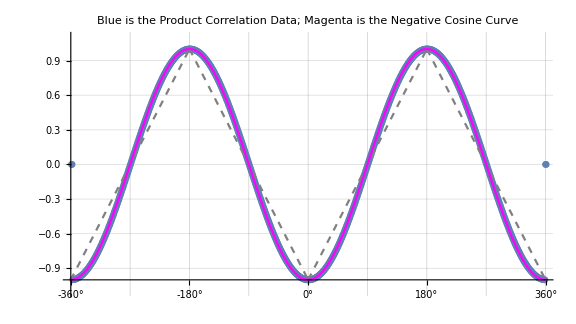

```mathematica
simulation=ListPlot[Eavg,PlotRange->{{3,717},{-1.1,1.1}},PlotMarkers->{Automatic,Small},AspectRatio->9/16,Ticks->{{{0,"-360°"},{90,"-270°"},{180,"-180°"},{270,"-90°"},{360,"0°"},{450,"90°"},{540,"180°"},{630,"270°"},{720,"360°"}},Automatic},
GridLines->Automatic,AxesOrigin->{0,-1.0},ImageSize->Large,PlotLabel->"Blue is the Product Correlation Data; Magenta is the Negative Cosine Curve",LabelStyle->Directive[Bold,Black]];
negcos=Plot[-Cos[x Degree],{x,1,720},PlotStyle->{Magenta}];
p1=Plot[-1+2x1 Degree/π,{x1,0,180},PlotStyle->{Gray,Dashed}];
p2=Plot[3-2x2 Degree/π,{x2,180,360},PlotStyle->{Gray,Dashed}];
p3=Plot[-1+2 (x3-360) Degree/π,{x3,360,540},PlotStyle->{Gray,Dashed}];
p4=Plot[3-2 (x4-360) Degree/π,{x4,540,720},PlotStyle->{Gray,Dashed}];
Show[ simulation,p1,p2,p3,p4, negcos]
```

Computing Averages

```mathematica
AveA=N[Total[A]/m];
AveB=N[Total[B]/m];
Print[" <A> = ",AveA,"  <B> = ",AveB];
meanpc=Expand[Mean[pc]];
Print["Cross products vanish, meanpc = ",meanpc];
```

<A> = -0.0012  <B> = 0.00756

Cross products vanish, meanpc = -8.61614×10^-20 e_2 e_3-2.22847×10^-19 e_2 e_4-0.000490095 e_3 e_4

The A and B averages  of the +/- 1 outcomes are to demonstrate 
that they match the quantum mechanical prediction.